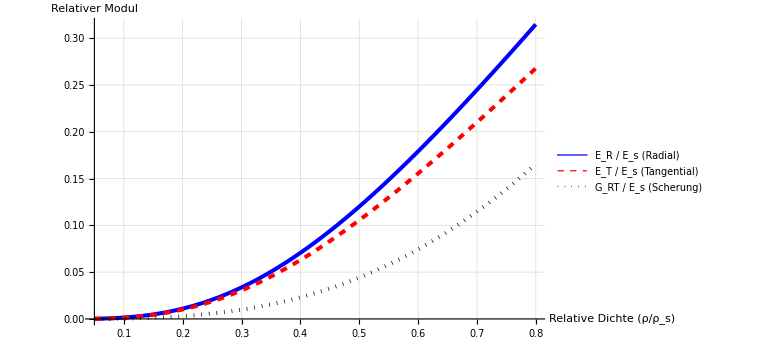

=== MAKROSKOPISCHE KENNWERTE DES HOMOGENISIERTEN JAHRESRINGS ===

Effektiver radialer Modul (E_R/E_s):      0.018

Effektiver tangentialer Modul (E_T/E_s):  0.0732

Effektiver Schermodul (G_RT/E_s):         0.0049

Resultierende makroskopische Anisotropie (E_R / E_T): 0.24

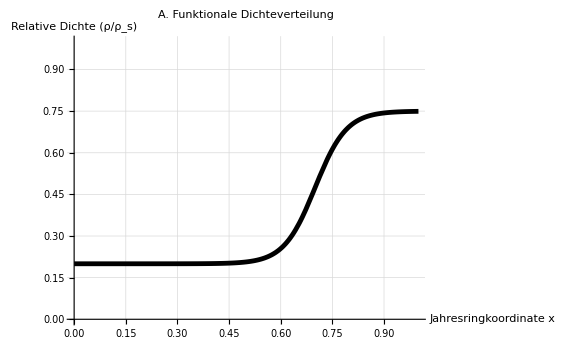
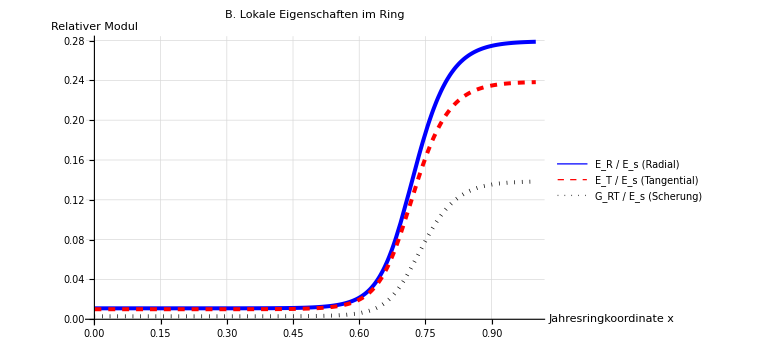
-Graphics- | -Graphics-

```mathematica
(* ====================================================================*)
(* Mikromechanisches Wabenmodell für Holz nach Gibson & Ashby *)
(* ====================================================================*)
ClearAll["Global`*"]

(* 1. Geometrische Beziehung: Verhältnis von Zellwanddicke (t) zu Länge (l) *)
(* für die relative Dichte rhoRel=rho/rho_s *)
tOverL[rhoRel_,theta_]:=(rhoRel*2*Cos[theta]*(1+Sin[theta]))/3

(* 2. Steifigkeitsfaktoren der Zellwände (relativ) *)
(*  K_f (Biegung) und K_s (Streckung) *)
Kf[rhoRel_,theta_]:=tOverL[rhoRel,theta]^3
Ks[rhoRel_,theta_]:=tOverL[rhoRel,theta]

(* ====================================================================*)
(* 3. Relative Elastizitätsmodule und Schubmodul *)
(* ====================================================================*)
(* Die Ergebnisse sind dimensionslos (Modul/Es) *)

(* Radiale Steifigkeit E_R/E_s *)
ERrel[rhoRel_,theta_]:=(1+Sin[theta])/(Cos[theta]*(Cos[theta]^2/Kf[rhoRel,theta]+(2+Sin[theta]^2)/Ks[rhoRel,theta]))

(* Tangentiale Steifigkeit E_T/E_s *)
ETrel[rhoRel_,theta_]:=1/((1+Cos[theta])*(Sin[theta]^2/Kf[rhoRel,theta]+Cos[theta]/Ks[rhoRel,theta]))

(* Transversaler Schubmodul G_RT/E_s *)
GRTrel[rhoRel_,theta_]:=1/(Cos[theta]*(3/(Kf[rhoRel,theta]*(1+Sin[theta]))+(1+Sin[theta])/(Ks[rhoRel,theta]*(Cos[theta]^2+(1+Sin[theta])*Sin[theta])^2)))

(* Querkontraktionszahl nu_RT *)
NuRT[rhoRel_,theta_]:=(Sin[theta]*Cos[theta]*(1/Kf[rhoRel,theta]-1/Ks[rhoRel,theta]))/(Cos[theta]*Sin[theta]^2/Kf[rhoRel,theta]+Cos[theta]/Ks[rhoRel,theta])


(* ====================================================================*)
(* 4. Visualisierung der Ergebnisse (Plot für theta=30 Grad)*)
(* ====================================================================*)

(* Winkel in Bogenmaß umrechnen *)
thetaRad=30*Degree;

Plot[{ERrel[rho,thetaRad],ETrel[rho,thetaRad],GRTrel[rho,thetaRad]},{rho,0.05,0.8},PlotStyle->{Directive[Blue,Thickness[0.005]],Directive[Red,Dashed,Thickness[0.005]],Directive[Black,Dotted,Thickness[0.005]]},PlotLegends->Placed[{"E_R / E_s (Radial)","E_T / E_s (Tangential)","G_RT / E_s (Scherung)"},Right],AxesLabel->{"Relative Dichte (ρ/ρ_s)","Relativer Modul"},ImageSize->Large,BaseStyle->{FontFamily->"Helvetica",FontSize->12},GridLines->Automatic]

(*====================================================================*)
(* 5. Jahresring-Skala (Kontinuierlicher Dichtegradient)*)
(* ====================================================================*)
(* x beschreibt die Position im Jahresring: 0=Start Frühholz, 1=Ende Spätholz*)

rhoFrueh=0.20;(* Geringe relative Dichte im Frühholz *)
rhoSpaet=0.75;(* Hohe relative Dichte im Spätholz *)
uebergangszone=0.70;(* Umschlagpunkt zum Spätholz bei 70% der Ringbreite *)
steilheit=22;(* Schärfe der Jahresringgrenze *)
rhoProfil[x_]:=rhoFrueh+(rhoSpaet-rhoFrueh)/(1+Exp[-steilheit*(x-uebergangszone)])

(* Lokale Eigenschaften entlang der Jahresringkoordinate x *)
ERlokal[x_]:=ERrel[rhoProfil[x],thetaRad]
ETlokal[x_]:=ETrel[rhoProfil[x],thetaRad]
GRTlokal[x_]:=GRTrel[rhoProfil[x],thetaRad]


(* ====================================================================*)
(* 6. Makroskopische Homogenisierung (Mischungsregeln)*)
(* ====================================================================*)
(* Numerische Integration über die gesamte Schichtstruktur des Jahresrings *)

(* RADIAL (R): Reihenschaltung der Phasen (Reuss-Grenzwert, konstante Spannung) *)
ERmacro=1/NIntegrate[1/ERlokal[x],{x,0,1}];

(* TANGENTIAL (T): Parallelschaltung der Phasen (Voigt-Grenzwert, konstante Dehnung) *)
ETmacro=NIntegrate[ETlokal[x],{x,0,1}];

(* SCHERUNG (RT): Scherspannung ist über die Schichten konstant *)
GRTmacro=1/NIntegrate[1/GRTlokal[x],{x,0,1}];

(* Textausgabe der makroskopischen Ergebnisse im Mathematica-Ausgabefenster *)
Print["=== MAKROSKOPISCHE KENNWERTE DES HOMOGENISIERTEN JAHRESRINGS ==="];
Print["Effektiver radialer Modul (E_R/E_s):      ",Round[ERmacro,0.0001]];
Print["Effektiver tangentialer Modul (E_T/E_s):  ",Round[ETmacro,0.0001]];
Print["Effektiver Schermodul (G_RT/E_s):         ",Round[GRTmacro,0.0001]];
Print["Resultierende makroskopische Anisotropie (E_R / E_T): ",Round[ERmacro/ETmacro,0.02]];


(* ====================================================================*)
(* 7. Visualisierung der Jahresring-Effekte *)
(* ====================================================================*)

plotDichte=Plot[rhoProfil[x],{x,0,1},PlotRange->{0,1},PlotStyle->{Directive[Black,Thickness[0.006]]},AxesLabel->{"Jahresringkoordinate x","Relative Dichte (ρ/ρ_s)"},PlotLabel->"A. Funktionale Dichteverteilung",GridLines->Automatic,BaseStyle->{FontFamily->"Helvetica",FontSize->12},ImageSize->Large];

plotModuleLokal=Plot[Evaluate[{ERlokal[x],ETlokal[x],GRTlokal[x]}],{x,0,1},PlotStyle->{Directive[Blue,Thickness[0.005]],Directive[Red,Dashed,Thickness[0.005]],Directive[Black,Dotted,Thickness[0.005]]},PlotLegends->Placed[{"E_R / E_s (Radial)","E_T / E_s (Tangential)","G_RT / E_s (Scherung)"},Right],AxesLabel->{"Jahresringkoordinate x","Relativer Modul"},PlotLabel->"B. Lokale Eigenschaften im Ring",GridLines->Automatic,BaseStyle->{FontFamily->"Helvetica",FontSize->12},ImageSize->Large];

(* Grid anstelle von GraphicsGrid verhindert das Quetschen durch die Legende*)
Grid[{{plotDichte,plotModuleLokal}}]
```